```mathematica
Remove["Global`*"]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[97][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[97]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

Define the expectation for a time-dependent Ornstein-Uhlenbeck process

```mathematica
Expand[( EX*Exp[(1-f)*T]-(X0)-(1-f)*Integrate[μ[t]*Exp[(1-f)*t],{t,0,T}])^2 == (1-f)^2*Integrate[Exp[2*(1-f)*t]*σ[t]^2,{t,0,T}]]
```

ⅇ^(2 (1-f) T) EX^2-2 ⅇ^((1-f) T) EX X0+X0^2-2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2==∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt

```mathematica
ESquareXFull= (∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt- (-2 ⅇ^((1-f) T) EX X0+X0^2-2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2))/ⅇ^(2 (1-f) T)
```

ⅇ^(-2 (1-f) T) (2 ⅇ^((1-f) T) EX X0-X0^2+2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt)

```mathematica
EXsol =  (X0)*Exp[-(1-f)*T]+(1-f)*Exp[-(1-f)*T]*Integrate[Exp[(1-f)*t]*μ[t],{t,0,T}]
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt

```mathematica
ESquareX=FullSimplify[ESquareXFull/.EX ->EXsol]
```

ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

```mathematica
SquareEX =FullSimplify[ ( EXsol)^2]
```

ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2

```mathematica
ESquareX
SquareEX
```

ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2

```mathematica
VarXFull=ESquareX-SquareEX
```

-ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

```mathematica
VarX = FullSimplify[VarXFull]
```

ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt

```mathematica
VarXv = ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) v[t]ⅆt
```

ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) {1,2,3,4}[t]ⅆt

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ((5-5 ⅇ^(T-f T))/(1-f)+(1-ⅇ^(T-f T) (Cos[T]+(-1+f) Sin[T]))/(2+(-2+f) f))

((-1+f) (-2+ⅇ^(2 (-1+f) T)-(-2+f) f+(-1+f)^2 Cos[2 T]-(-1+f) Sin[2 T]))/(4 (2+(-2+f) f))

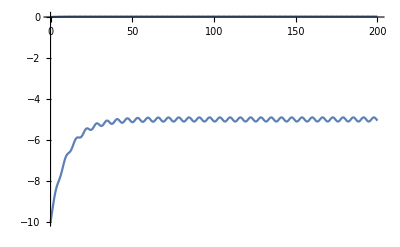

```mathematica
EXspecific = EXsol/.{μ[t]->-5+Sin[t],σ[t]->Sin[t]}
VarXSpecific=VarX/.{μ[t]->-5+Sin[t],σ[t]->Sin[t]}
Plot[{EXspecific,VarXSpecific}/.{f->0.9,X0->-10,μ0->0.5},{T,0,200}]
```

{-10 ⅇ^(-0.01 T)+0.01 ⅇ^(-0.01 T) (101.-100. ⅇ^(0.01 T)+ⅇ^(0.01 T) (-0.9999 Cos[T]+0.009999 Sin[T])),-ⅇ^(-0.02 T) (-10+0.01 (101.-100. ⅇ^(0.01 T)+ⅇ^(0.01 T) (-0.9999 Cos[T]+0.009999 Sin[T])))^2+ⅇ^(-0.02 T) ((-10+0.01 (101.-100. ⅇ^(0.01 T)+ⅇ^(0.01 T) (-0.9999 Cos[T]+0.009999 Sin[T])))^2+0.0004 (-72.9983+ⅇ^(0.02 T) (75.-1.9992 Cos[T]-0.00249975 Cos[2. T]+0.039984 Sin[T]-0.249975 Sin[2. T])))}

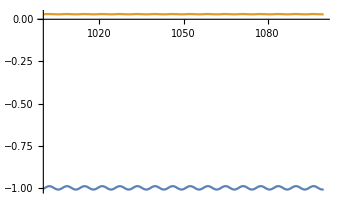

```mathematica
ExpVar = {EXspecific = EXsol,VarXSpecific=VarXFull}/.{μ[t]->-1+Sin[t],σ[t]->2+2*Sin[t],f->0.99,X0->-10,μ0->0.5}
Plot[ExpVar,{T,1000,1100}]
```

```mathematica
EXsol/.{μ[t]->-1+Sin[t],σ[t]->2*Sin[t],f->0.5,X0->-10,μ0->0.5}
```

-10 ⅇ^(-0.5 T)+0.5 ⅇ^(-0.5 T) (2.8-2. ⅇ^(0.5 T)+ⅇ^(0.5 T) (-0.8 Cos[T]+0.4 Sin[T]))

```mathematica
FullSimplify[%]
```

-1.-8.6 ⅇ^(-0.5 T)-0.4 Cos[T]+0.2 Sin[T]

```mathematica
EXsol
VarX
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt

ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt

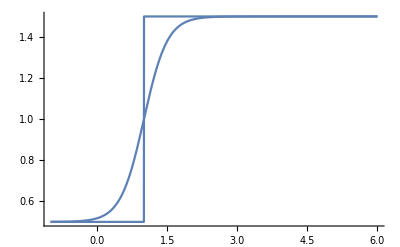

```mathematica
Show[
Plot[a1+HeavisideTheta[t-b1]/.{a1->0.5,b1->1},{t,-1,6}],
Plot[a1+1/(1+Exp[-2*k*(t-b1)])/.{k->2,a1->0.5,b1->1},{t,-1,6}]
]
```

```mathematica
EXHeavy = EXsol/.{μ[t]->a1+HeavisideTheta[t-b1],σ[t]->a2+HeavisideTheta[t-b2]}
VarXHeavy=VarX/.{μ[t]->a1+HeavisideTheta[t-b1],σ[t]->a2+HeavisideTheta[t-b2]}
EXLogistic = EXsol/.{μ[t]->a1+1/(1+Exp[-2*k*(t-b1)]),σ[t]->a2+1/(1+Exp[-2*k*(t-b2)])}
VarXLogistic=VarX/.{μ[t]->a1+1/(1+Exp[-2*k*(t-b1)]),σ[t]->a2+1/(1+Exp[-2*k*(t-b2)])}
```

ConditionalExpression[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+1/(-1+f)ⅇ^(-f (b1+T)) (-(ⅇ^(b1 f+T)-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])))),T∈Reals]

ConditionalExpression[1/2 ⅇ^(-2 b2 (-1+f)+2 (-1+f) T) (-1+f) (a2^2 (ⅇ^(2 b2 (-1+f))-ⅇ^(2 (-1+f) (b2-T)))-(1+2 a2) (-1+ⅇ^(2 (-1+f) (b2-T))) HeavisideTheta[T] HeavisideTheta[-b2+T]+(1+2 a2) HeavisideTheta[-b2] ((-1+ⅇ^(2 b2 (-1+f))) HeavisideTheta[T] HeavisideTheta[-b2+T]+HeavisideTheta[-T] (-1+ⅇ^(2 b2 (-1+f))-(-1+ⅇ^(2 (-1+f) (b2-T))) HeavisideTheta[-b2+T]))),T∈Reals]

ConditionalExpression[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)-(-1+Hypergeometric2F1[1,-(-1+f)/(2 k),(1-f+2 k)/(2 k),-ⅇ^(-2 b1 k)])/(-1+f)+(ⅇ^(T-f T) (-1+Hypergeometric2F1[1,-(-1+f)/(2 k),(1-f+2 k)/(2 k),-ⅇ^(2 k (-b1+T))]))/(-1+f)),ⅇ^(-2 b1 k)≥-1&&ⅇ^(2 k (-b1+T))≥-1]

$Aborted

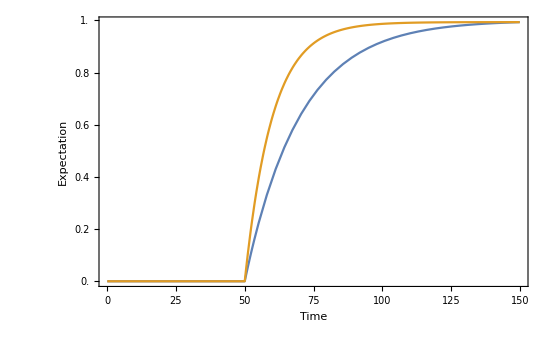

```mathematica
Show[
TwoAxisPlot[{EXHeavy,VarXHeavy}/.{f->0.95,X0->0,a1->0,b1->50,a2->0,b2->50},{T,0,150}],FrameLabel->{"Time","Expectation","","Variance"}]
```

```mathematica
D[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+1/(-1+f)ⅇ^(-f (b1+T)) (-(ⅇ^(b1 f+T)-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])))),T]
```

ⅇ^((-1+f) T) (-1+f) X0+ⅇ^((-1+f) T) (1-f) (-1+f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+1/(-1+f)ⅇ^(-f (b1+T)) ((-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T]))))+ⅇ^((-1+f) T) (1-f) (a1 ⅇ^(T-f T)-1/(-1+f)ⅇ^(-f (b1+T)) f ((-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])))+1/(-1+f)ⅇ^(-f (b1+T)) ((-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) DiracDelta[-b1+T] HeavisideTheta[T]+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) DiracDelta[T] HeavisideTheta[-b1+T]+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T) f) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) DiracDelta[-b1+T] HeavisideTheta[T]+(ⅇ^(f (b1+T))-ⅇ^(b1+f T)) DiracDelta[T] HeavisideTheta[-b1+T]+(ⅇ^(f (b1+T)) f-ⅇ^(b1+f T) f) HeavisideTheta[T] HeavisideTheta[-b1+T]-DiracDelta[T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])+HeavisideTheta[-T] (ⅇ^(f (b1+T)) f-ⅇ^(b1+f T) f+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) DiracDelta[-b1+T]+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T) f) HeavisideTheta[-b1+T]))))

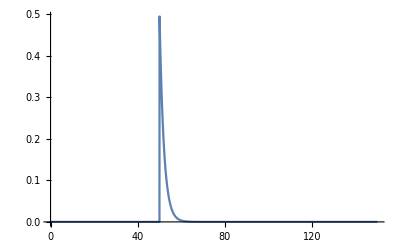

```mathematica
Plot[%218/.{X0->0,a1->0,b1->50,f->0.5},{T,0,150},PlotRange->All]
```

```mathematica
NSolve[D[EXHeavy,T]==0/.{X0->0,a1->0,b1->50,f->0.5},T]
```

NSolve[ConditionalExpression[0.-0.25 ⅇ^(-0.5 T) (0.+2. ⅇ^(-0.5 (50+T)) (-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) HeavisideTheta[-50+T] HeavisideTheta[T])+0.5 ⅇ^(-0.5 T) (-1. ⅇ^(-0.5 (50+T)) (-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) HeavisideTheta[-50+T] HeavisideTheta[T]-2. ⅇ^(-0.5 (50+T)) (-(-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) DiracDelta[T] HeavisideTheta[-50+T]-(-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) DiracDelta[-50+T] HeavisideTheta[T]-(-0.5 ⅇ^(50+0.5 T)+ⅇ^(25.+T)) HeavisideTheta[-50+T] HeavisideTheta[T]))==0,T∈Reals],T]

```mathematica
EXSin = EXsol/.{μ[t]->a1+b1*Sin[ω1*t],v[t]->a2+b2*Sin[ω2*t]}
VarXSin=VarXv/.{μ[t]->a1+b1*Sin[ω1*t],v[t]->a2+b2*Sin[ω2*t]}
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+(ⅇ^(-f T) (b1 ⅇ^(f T) ω1-b1 ⅇ^T (ω1 Cos[T ω1]+(-1+f) Sin[T ω1])))/((-1+f)^2+ω1^2))

ⅇ^(2 (-1+f) T) (-1+f)^2 ((a2 (-1+ⅇ^(-2 (-1+f) T)))/(2-2 f)+(b2 ⅇ^(-2 (-1+f) T) (ⅇ^(2 (-1+f) T) ω2-ω2 Cos[T ω2]-2 (-1+f) Sin[T ω2]))/(4-8 f+4 f^2+ω2^2))

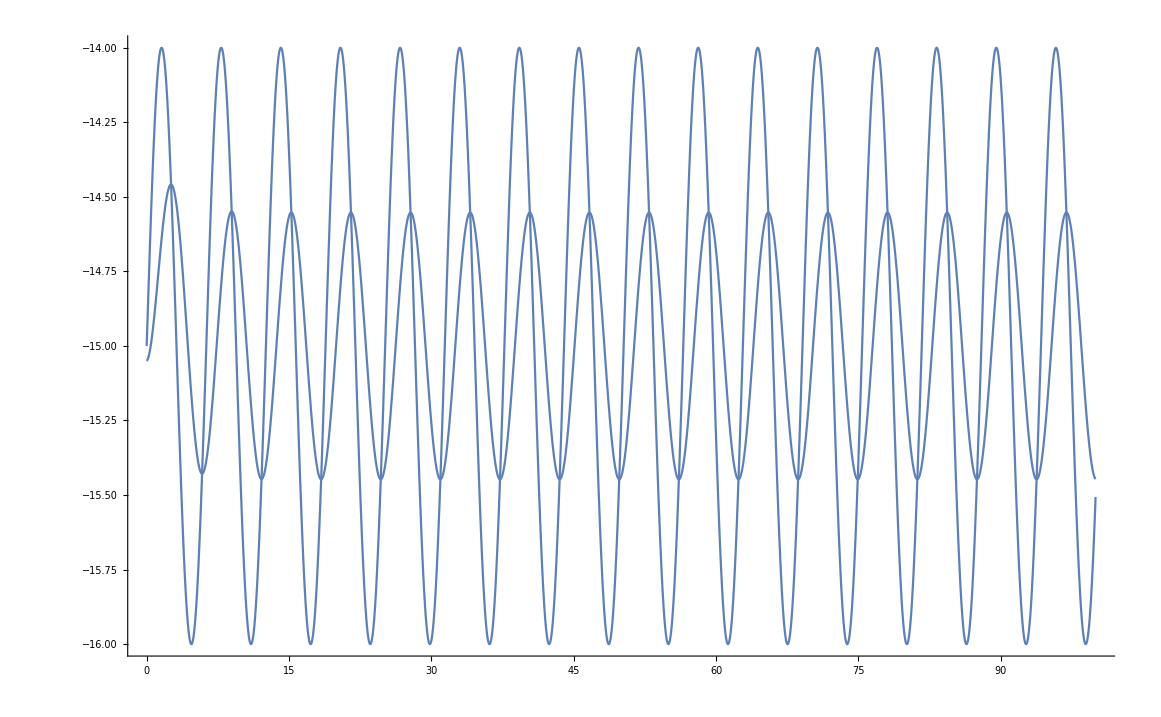

```mathematica
Plot[{EXSin,a1+b1*Sin[ω1 T]}/.{X0->-15.05,a1->-15,b1->1,ω1->1,f->0.5},{T,0,100}]
```

```mathematica
FullSimplify[EXSin]
FullSimplify[VarXSin]
```

ⅇ^((-1+f) T) (X0+(ⅇ^(-f T) (-b1 ⅇ^(f T) (-1+f) ω1+a1 (ⅇ^T-ⅇ^(f T)) ((-1+f)^2+ω1^2)+b1 ⅇ^T (-1+f) (ω1 Cos[T ω1]+(-1+f) Sin[T ω1])))/((-1+f)^2+ω1^2))

1/4 ⅇ^(2 (-1+f) T) (-1+f)^2 ((2 a2^2+b2^2)/(-1+f)-(b2^2 (-1+f))/((-1+f)^2+ω2^2)+(8 a2 b2 ω2)/(4 (-1+f)^2+ω2^2)+ⅇ^(-2 (-1+f) T) ((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4 (-1+f)^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/((-1+f)^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4 (-1+f)^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/((-1+f)^2+ω2^2)))

```mathematica
Assuming[f<=1&&f>0,Limit[EXSin,T->Infinity]]
```

Limit[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+(ⅇ^(-f T) (b1 ⅇ^(f T) ω1-b1 ⅇ^T (ω1 Cos[T ω1]+(-1+f) Sin[T ω1])))/((-1+f)^2+ω1^2)),T→∞]

```mathematica
EXSinStationary = FullSimplify[a1+(-b1*(1-f) *(ω1 Cos[T ω1]+(-1+f) Sin[T ω1]))/((-1+f)^2+ω1^2)]
VarXSinStationary=FullSimplify[1/4 (-1+f)^2((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4 (-1+f)^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/((-1+f)^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4 (-1+f)^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/((-1+f)^2+ω2^2))]
```

a1+(b1 (-1+f) (ω1 Cos[T ω1]+(-1+f) Sin[T ω1]))/((-1+f)^2+ω1^2)

1/4 (-1+f)^2 ((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4 (-1+f)^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/((-1+f)^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4 (-1+f)^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/((-1+f)^2+ω2^2))

```mathematica
Manipulate[
Plot[{EXSin,EXSinStationary,
a1+b1*Sin[ω1*T]}/.{a1->1,b1->0.5,X0->-10,f->F,ω1->Omega1},{T,5500,5550},PlotRange->{-1,3}],
{F,0,0.99},{Omega1,0,2Pi}]
```

```mathematica
Manipulate[
Plot[{EXSin}/.{a1->1,b1->1,X0->-10,f->F,ω1->Omega1},{T,90,100},PlotRange->{-1,3}],
{F,0.0001,0.99},{Omega1,0,2Pi}]
```

```mathematica
(-b1*(1-f)*w1)^2
```

b1^2 (1-f)^2 w1^2

```mathematica
FullSimplify[Sqrt[b1^2*(1+(1-f)^2 w1^2)]]
```

√(b1^2 (1+(-1+f)^2 w1^2))

```mathematica
FullSimplify[(√(b1^2 (1+(-1+f)^2 w1^2)))/((f-1)^2+w1^2)]
```

(√(b1^2 (1+(-1+f)^2 w1^2)))/((-1+f)^2+w1^2)

EXStationary = a1 + (b1*λ)/(√(λ^2+ω^2))*Sin[ω t + ArcTan[ω/λ]];
VarXStationary = 1/4 λ(2 a2^2+b2^2) + (2a2 b2 λ^2)/(√(4 λ^2+ω^2))Sin[ω t + ArcTan[ω/(2λ)]] - (b2^2 λ^2)/(4 √(λ^2+ω^2))Sin[2ω t + ArcTan[λ/ω]]/.{a2→Sqrt[aa2],b2→Sqrt[bb2]};

FROM Notes...

```mathematica
EXStationary = a1 + (b1*λ)/(√(λ^2+ω^2))*Sin[ω t + ArcTan[ω/λ]];
VarXStationary = 1/4 λ(2 a2^2+b2^2) + (2a2 b2 λ^2)/(√(4 λ^2+ω^2))Sin[ω t + ArcTan[ω/(2λ)]] - (b2^2 λ^2)/(4 √(λ^2+ω^2))Sin[2ω t + ArcTan[λ/ω]]/.{a2->Sqrt[aa2],b2->Sqrt[bb2]};
```

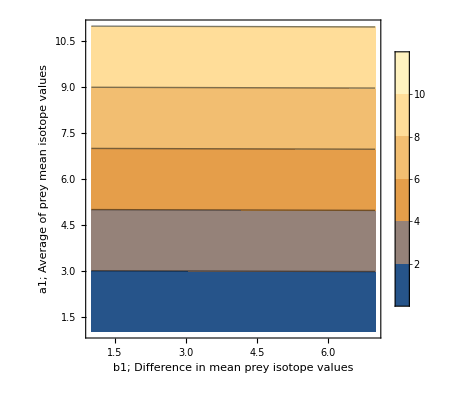
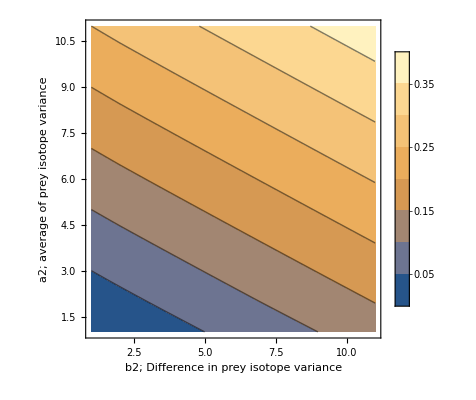
-Graphics- | -Graphics-

```mathematica
AvgDiffPlot = Grid[{{
ListContourPlot[Mean[Table[Table[EXStationary,{a1,0,10,1},{b1,0,2Pi,1}]/.{ω->0.2,λ->0.05},{t,100,1000,20}]],PlotLegends->True,FrameLabel->{"b1; Difference in mean prey isotope values","a1; Average of prey mean isotope values"}],
ListContourPlot[Mean[Table[Table[VarXStationary,{aa2,0,10,1},{bb2,0,10,1}]/.{ω->0.2,λ->0.05},{t,100,1000,20}]],PlotLegends->True,
FrameLabel->{"b2; Difference in prey isotope variance","a2; average of prey isotope variance"}]}},Spacings->{1,0}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_AvgDiff.pdf",AvgDiffPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_AvgDiff.pdf

Plot 1) The mean increases with the mean!; The amplitude of diet switch does not affect the mean of the consumer’s isotope values
Plot 2) 
	i) As you increase the average variance of prey isotope values, the mean isotopic variance of the consumer increases linearly
	ii) As you increase the amplitude of the variance (effectively saying that your switching between 2 prey with very different isotopic variances ~ heterogeneity of prey isotope variance), you increase consumer isotope variance.

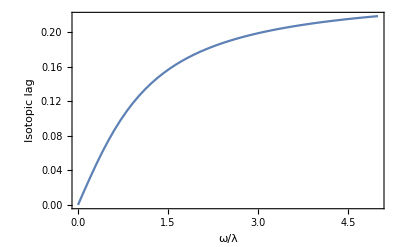

```mathematica
OffsetPlot=Plot[ArcTan[r]/(2Pi),{r,0,5},PlotRange->All,Frame->True,FrameLabel->{"ω/λ","Isotopic lag"}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_Offset.pdf",OffsetPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_Offset.pdf

How does mean and variance change given differnt omega/lambda when switching between 2 different diets in the sea otter system?

```mathematica
mu = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
sig = {1.0,0.9,0.7,0.9,0.9,0.9,0.5,1.1,0.8,1.1,1.4,1.0};
nprey = Length[mu];
Diet1 = {1,1,1,1,1,1,1,1,1,100,1,1};
Diet2 = {1,1,1,1,1,1,1,1,1,1,1,1};
EZ1 =With[{Diet=Diet1}, N[Sum[Diet[[i]]/Total[Diet]*mu[[i]],{i,1,nprey}]]];
EZ2 = With[{Diet=Diet2},N[Sum[Diet[[i]]/Total[Diet]*mu[[i]],{i,1,nprey}]]];
VarZ1 = With[{Diet=Diet1},N[Sum[Diet[[i]]/Total[Diet](sig[[i]]^2+mu[[i]]^2) - (Diet[[i]]^2 *mu[[i]]^2)/Total[Diet]^2,{i,1,nprey}] - Sum[(Diet[[i]]*Diet[[j]]*mu[[i]]*mu[[j]])/Total[Diet]^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]]];
VarZ2 =  With[{Diet=Diet2},N[Sum[Diet[[i]]/Total[Diet](sig[[i]]^2+mu[[i]]^2) - (Diet[[i]]^2 *mu[[i]]^2)/Total[Diet]^2,{i,1,nprey}] - Sum[(Diet[[i]]*Diet[[j]]*mu[[i]]*mu[[j]])/Total[Diet]^2 Boole[i≠j],{i,1,nprey},{j,1,nprey}]]];
A1 = (EZ1 + EZ2)/2;
B1 = Abs[(EZ1 - EZ2)]/2;
A2 = (VarZ1 + VarZ2)/2;
B2 = Abs[(VarZ1 - VarZ2)]/2;
```

```mathematica
ESin = ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+(ⅇ^(-f T) (b1 ⅇ^(f T) ω1-b1 ⅇ^T (ω1 Cos[T ω1]+(-1+f) Sin[T ω1])))/((-1+f)^2+ω1^2));
VarSin =ⅇ^(2 (-1+f) T) (-1+f)^2 ((a2 (-1+ⅇ^(-2 (-1+f) T)))/(2-2 f)+(b2 ⅇ^(-2 (-1+f) T) (ⅇ^(2 (-1+f) T) ω2-ω2 Cos[T ω2]-2 (-1+f) Sin[T ω2]))/(4-8 f+4 f^2+ω2^2));
```

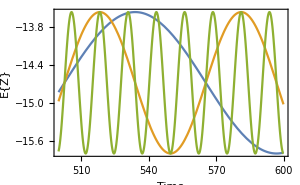
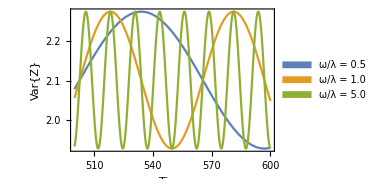
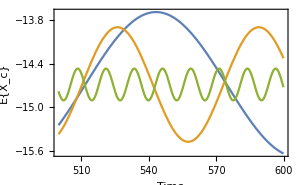
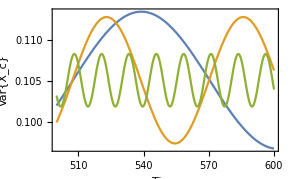

```mathematica
Tstart=500;
Tterm= 600;
Xstart = 0;
EVarTempPlot=
Column[{
Row[{
Show[{
Plot[a1+b1*Sin[ω t]/.{a1->A1,b1->B1,ω->0.05,λ->0.1},{t,Tstart,Tterm},PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","E{Z}"}],
Plot[a1+b1*Sin[ω t]/.{a1->A1,b1->B1,ω->0.1,λ->0.1},{t,Tstart,Tterm},PlotStyle->ColorData[97,2]],
Plot[a1+b1*Sin[ω t]/.{a1->A1,b1->B1,ω->0.5,λ->0.1},{t,Tstart,Tterm},PlotStyle->ColorData[97,3]]
},ImageSize->300],
Show[{
Plot[a2+b2*Sin[ω t]/.{a2->A2,b2->B2,ω->0.05,λ->0.1},{t,Tstart,Tterm},PlotRange->All,PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","Var{Z}"}],
Plot[a2+b2*Sin[ω t]/.{a2->A2,b2->B2,ω->0.1,λ->0.1},{t,Tstart,Tterm},PlotStyle->ColorData[97,2]],
Plot[a2+b2*Sin[ω t]/.{a2->A2,b2->B2,ω->0.5,λ->0.1},{t,Tstart,Tterm},PlotStyle->ColorData[97,3],
PlotLegends->SwatchLegend[Table[ColorData[97,i],{i,1,3}],{"ω/λ = 0.5","ω/λ = 1.0","ω/λ = 5.0"},LegendFunction->None,LegendMargins->1,LegendLayout->{"Column",1},LegendMarkers->"Bubble"]]
},ImageSize->290]
}],
Row[{
Show[{
Plot[EXSin/.{X0->Xstart,a1->A1,b1->B1,ω1->0.05,f->0.9},{T,Tstart,Tterm},PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","E{X_c}"}],
Plot[EXSin/.{X0->Xstart,a1->A1,b1->B1,ω1->0.1,f->0.9},{T,Tstart,Tterm},PlotStyle->ColorData[97,2]],
Plot[EXSin/.{X0->Xstart,a1->A1,b1->B1,ω1->0.5,f->0.9},{T,Tstart,Tterm},PlotStyle->ColorData[97,3]]
},ImageSize->300],
Show[{
Plot[VarXSin/.{X0->Xstart,a2->A2,b2->B2,ω2->0.05,f->0.9},{T,Tstart,Tterm},PlotRange->All,PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","Var{X_c}"}],
Plot[VarXSin/.{X0->Xstart,a2->A2,b2->B2,ω2->0.1,f->0.9},{T,Tstart,Tterm},PlotStyle->ColorData[97,2]],
Plot[VarXSin/.{X0->Xstart,a2->A2,b2->B2,ω2->0.5,f->0.9},{T,Tstart,Tterm},PlotStyle->ColorData[97,3](*,
PlotLegends->SwatchLegend[Table[ColorData[97,i],{i,1,3}],{"ω/λ = 0.5","ω/λ = 1.0","ω/λ = 2.0"},LegendFunction->None,LegendMargins->1,LegendLayout->{"Column",1},LegendMarkers->"Bubble"]*)]
},ImageSize->290]
}]
}]
```

```mathematica
0.5/0.1
```

5.

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_EVarTemp.pdf",EVarTempPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_EVarTemp.pdf

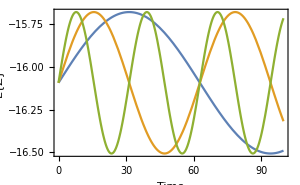
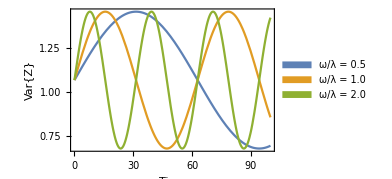
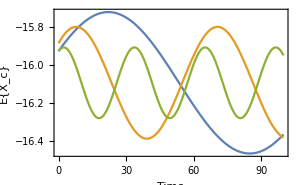
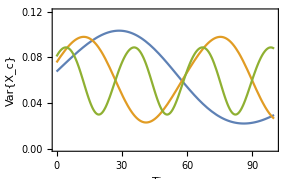

```mathematica
(*EVarTempPlot=
Tterm= 100;
Column[{
Row[{
Show[{
Plot[a1+b1*Sin[ω t]/.{a1->A1,b1->B1,ω->0.05,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","E{Z}"}],
Plot[a1+b1*Sin[ω t]/.{a1->A1,b1->B1,ω->0.1,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,2]],
Plot[a1+b1*Sin[ω t]/.{a1->A1,b1->B1,ω->0.2,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,3]]
},ImageSize->300],
Show[{
Plot[Sqrt[aa2]+Sqrt[bb2]*Sin[ω t]/.{aa2->AA2,bb2->BB2,ω->0.05,λ->0.1},{t,0,Tterm},PlotRange->All,PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","Var{Z}"}],
Plot[Sqrt[aa2]+Sqrt[bb2]*Sin[ω t]/.{aa2->AA2,bb2->BB2,ω->0.1,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,2]],
Plot[Sqrt[aa2]+Sqrt[bb2]*Sin[ω t]/.{aa2->AA2,bb2->BB2,ω->0.2,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,3],
PlotLegends->SwatchLegend[Table[ColorData[97,i],{i,1,3}],{"ω/λ = 0.5","ω/λ = 1.0","ω/λ = 2.0"},LegendFunction->None,LegendMargins->1,LegendLayout->{"Column",1},LegendMarkers->"Bubble"]]
},ImageSize->290]
}],
Row[{
Show[{
Plot[EXStationary/.{a1->A1,b1->B1,ω->0.05,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","E{X_c}"}],
Plot[EXStationary/.{a1->A1,b1->B1,ω->0.1,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,2]],
Plot[EXStationary/.{a1->A1,b1->B1,ω->0.2,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,3]]
},ImageSize->300],
Show[{
Plot[VarXStationary/.{aa2->AA2,bb2->BB2,ω->0.05,λ->0.1},{t,0,Tterm},PlotRange->{0,0.12},PlotStyle->ColorData[97,1],
Frame->True,FrameLabel->{"Time","Var{X_c}"}],
Plot[VarXStationary/.{aa2->AA2,bb2->BB2,ω->0.1,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,2]],
Plot[VarXStationary/.{aa2->AA2,bb2->BB2,ω->0.2,λ->0.1},{t,0,Tterm},PlotStyle->ColorData[97,3](*,
PlotLegends->SwatchLegend[Table[ColorData[97,i],{i,1,3}],{"ω/λ = 0.5","ω/λ = 1.0","ω/λ = 2.0"},LegendFunction->None,LegendMargins->1,LegendLayout->{"Column",1},LegendMarkers->"Bubble"]*)]
},ImageSize->290]
}]
}]*)
```